```mathematica
SetDirectory[NotebookDirectory[]]
(*Tmax=0.3/J*20;*)
Tnum=1000;
(*Tmax=.8Tmax;*)


Pnat=Import["N30.wdx"];
ListDensityPlot[Pnat⟦;;,1,;;⟧,PlotRange->All,InterpolationOrder->0,PlotLabel->"P_(n, -1)(t)"]
ListDensityPlot[Pnat⟦;;,2,;;⟧,PlotRange->All,InterpolationOrder->0,PlotLabel->"P_(n, 0)(t)"]
ListDensityPlot[Pnat⟦;;,3,;;⟧,PlotRange->All,InterpolationOrder->0,PlotLabel->"P_(n, +1)(t)"]
ListPlot[{Pnat⟦1,1,;;⟧,Pnat⟦1,2,;;⟧,Pnat⟦1,3,;;⟧},PlotRange->All,InterpolationOrder->0,PlotLabels->{"P_(n = 1, -1)(t)","P_(n = 1, 0)(t)","P_(n = 1, +1)(t)"}]
```

/Users/steven/Nextcloud/NetDisk/Works/24.08.19 NonBoltz/Code/scale

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
pp={}; n0=1; a0=3;
Do[
file=StringJoin[{"N",ToString[n],".wdx"}];
Pnat=Import[file];
AppendTo[pp,Pnat⟦n0,a0,;;⟧],
{n,10,30}]

Export["sca.csv",pp]
```

sca.csv

```mathematica
p1=Import["N10.wdx"];
p2=Import["N20.wdx"];
p3=Import["N30.wdx"];

ps=Join[p1⟦1⟧,p2⟦1⟧,p3⟦1⟧];
Export["ps123.csv",ps,"CSV"]
```

ps123.csv

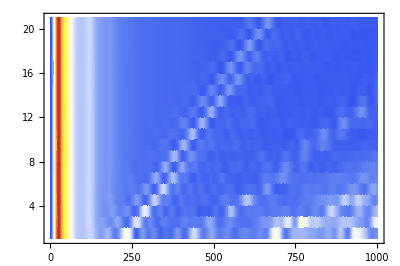

-Graphics3D-

-Graphics-

```mathematica
ListDensityPlot[pp,InterpolationOrder->0,PlotRange->All,AspectRatio->1/1.5,ColorFunction->"TemperatureMap"]
ListPlot3D[pp,PlotRange->All]
ListLinePlot[{pp⟦1⟧,pp⟦11⟧,pp⟦21⟧},PlotLabels->{10,20,30},PlotRange->All,Mesh->All]
```

```mathematica
Pnat=Import["N30.wdx"];
a=2;NN=30;
Tnum=Length[Pnat⟦1,1,;;⟧];
EntroS[P_]:=Sum[
If[0<P⟦n⟧<1,-P⟦n⟧Log[P⟦n⟧],0],{n,1,Length[P]}];
```

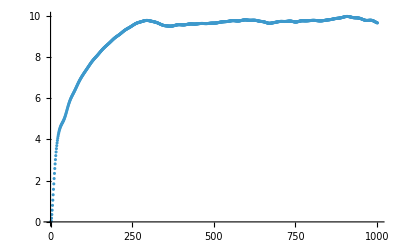

{8,7,8,11,36,59,83,107,130,152,174,196,218,240,262,296,299,296,262,240,218,196,174,152,130,107,83,59,36,11}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Propagating by  Subscript[P, n,a](t)  *)

Snt=ParallelTable[EntroS[Pnat⟦n,;;,t⟧],
{n,1,NN},{t,1,Tnum}]; (* Entropy Subscript[S, n](t) *)
St=Table[Total[Snt⟦;;,t⟧],{t,1,Tnum}];
ListPlot[St,PlotRange->All]

(* Subscript[S, n]'(t), Subscript[S, n]''(t), and find out first zero position of Subscript[S, n]''(t),
namely, the (first) fastest increasing t of Subscript[S, n](t) *)

DSnt=Table[Snt⟦n,t+1⟧-Snt⟦n,t⟧,{n,1,NN},{t,1,Tnum-1}];
DDSnt=Table[DSnt⟦n,t+1⟧-DSnt⟦n,t⟧,{n,1,NN},{t,1,Tnum-2}];
TidxSv=Table[tid=1;
Do[
If[Snt⟦n,t⟧>10^-12 && DDSnt⟦n,t⟧<0,tid=t;Break[] ],{t,1,Tnum-2}];
tid,
{n,1,NN}]
ListDensityPlot[Snt,PlotRange->All,InterpolationOrder->0]
ListDensityPlot[Pnat⟦;;,1,;;⟧,PlotRange->All,InterpolationOrder->0]
ListDensityPlot[Pnat⟦;;,2,;;⟧,PlotRange->All,InterpolationOrder->0]
ListDensityPlot[Pnat⟦;;,3,;;⟧,PlotRange->All,InterpolationOrder->0]
```

{1,1,1,19,44,69,94,118,141,163,185,207,229,251,272,307,305,307,272,251,229,207,185,163,141,118,94,69,44,19}

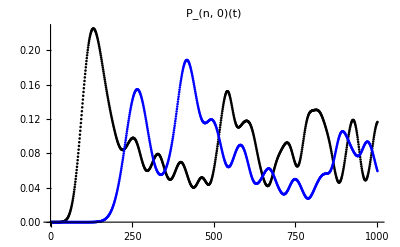

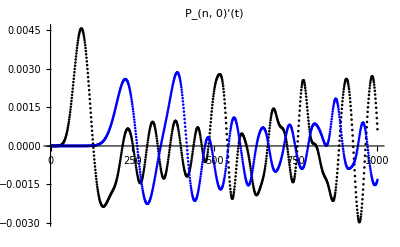

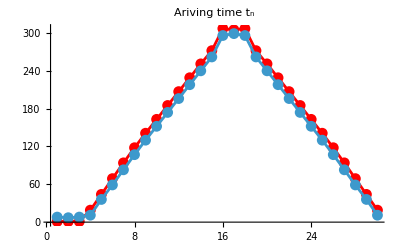

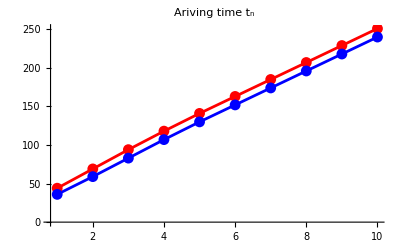

```mathematica
a=2;
Dpnt=Table[Pnat⟦n,a,t+1⟧-Pnat⟦n,a,t⟧,{n,1,NN},{t,1,Tnum-1}];
DDpnt=Table[Dpnt⟦n,t+1⟧-Dpnt⟦n,t⟧,{n,1,NN},{t,1,Tnum-2}];
TidxPv=Table[tid=1;
Do[
If[Pnat⟦n,2,t⟧>10^-12 && DDpnt⟦n,t⟧<0,tid=t;Break[] ],{t,1,Tnum-2}];
tid,
{n,1,NN}]

n1=7;n2=13;
ListPlot[{Pnat[[n1,a,;;]],Pnat[[n2,a,;;]]},PlotRange->All,PlotStyle->{Black,Blue},PlotLabel->"P_(n, 0)(t)"]
ListPlot[{Dpnt[[n1,;;]],Dpnt[[n2,;;]]},PlotRange->All,PlotStyle->{Black,Blue},PlotLabel->"P_(n, 0)'(t)"]
vp=ListLinePlot[TidxPv,PlotRange->All,PlotLabel->"Ariving time t_n",Mesh->All,PlotStyle->Red];
vs=ListLinePlot[TidxSv,PlotRange->All,PlotLabel->"Ariving time t_n",Mesh->All];


Show[vp,vs]
ListLinePlot[{TidxPv⟦5;;14⟧,TidxSv⟦5;;14⟧},PlotRange->All,PlotLabel->"Ariving time t_n",Mesh->All,PlotStyle->{Red,Blue}]
Manipulate[ListPlot[Pnat[[n1,a,;;]],PlotRange->All],{n1,1,NN,1}]
Manipulate[ListPlot[Snt[[n1,;;]],PlotRange->All],{n1,1,NN,1}]
```

```mathematica
n1=5;n2=14;
lp=LinearModelFit[Transpose[{Range[n1,n2],TidxPv⟦n1;;n2⟧}],x,x]
ls=LinearModelFit[Transpose[{Range[n1,n2],TidxSv⟦n1;;n2⟧}],x,x]
lp["ANOVATable"]
ls["ANOVATable"]

n1=6;n2=13;
lp=LinearModelFit[Transpose[{Range[n1,n2],TidxPv⟦n1;;n2⟧}],x,x]
ls=LinearModelFit[Transpose[{Range[n1,n2],TidxSv⟦n1;;n2⟧}],x,x]
lp["ANOVATable"]
ls["ANOVATable"]
```

FittedModel[…]

FittedModel[…]

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 43092.2 | 43092.2 | 11245.9 | 6.9844×10^-14
Error | 8 | 30.6545 | 3.83182 |  | 
Total | 9 | 43122.9 |  |  |

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 42318.7 | 42318.7 | 24521.8 | 3.09384×10^-15
Error | 8 | 13.8061 | 1.72576 |  | 
Total | 9 | 42332.5 |  |  |

FittedModel[…]

FittedModel[…]

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 21669.4 | 21669.4 | 10770.6 | 5.39447×10^-11
Error | 6 | 12.0714 | 2.0119 |  | 
Total | 7 | 21681.5 |  |  |

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 21510.7 | 21510.7 | 15826.9 | 1.70093×10^-11
Error | 6 | 8.15476 | 1.35913 |  | 
Total | 7 | 21518.9 |  |  |

```mathematica
Join[{{1,2,3}},{{5,6,7}}]
```

{{1,2,3},{5,6,7}}

```mathematica
{TidxSv⟦5⟧,TidxSv⟦10⟧,TidxSv⟦15⟧}*40./1000
t30=22.7143*30*40./1000
t10=t30/3.
```

{1.44,6.08,10.48}

27.2572

9.08572